## Two-state mixing

```mathematica
(*The interaction strength between the two states*)
VINT=0.05;
(*The initial separation between the two states*)
DE21=0.1;
RR[de21_,vint_]:=de21/vint;
(*the smaller mixing amplitude β*)
β[r_]:=1/((1+(r/2+Sqrt[1+r^2/4])^2)^(1/2));
```

```mathematica
invbeta[x_]:=InverseFunction[β][x];
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

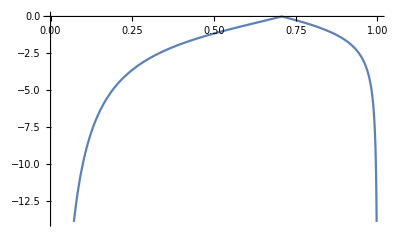

```mathematica
Plot[invbeta[x],{x,0,1}]
```

```mathematica
f0=1/((1+(#/2+Sqrt[1+#^2/4])^2)^(1/2))&;
g0=InverseFunction[f0]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

-(√(-1+4 #1^2-4 #1^4))/(√(-#1^2+#1^4))&

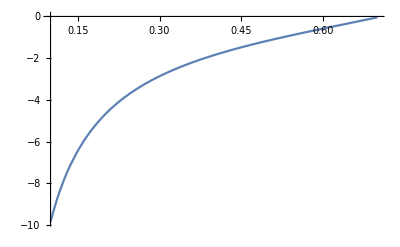

```mathematica
Plot[g0[x],{x,0.1,0.7}]
```

```mathematica
InverseFunction[ConditionalExpression[1/((1+(#/2+Sqrt[1+#^2/4])^2)^(1/2)),0.1<#1<12]&][b]
```

ConditionalExpression[√((-1.+4. b^2-4. b^4)/(b^2 (-1.+b^2))), 0.0824805<b<0.689225]